## a few models plot

### plot x Log (1/x)

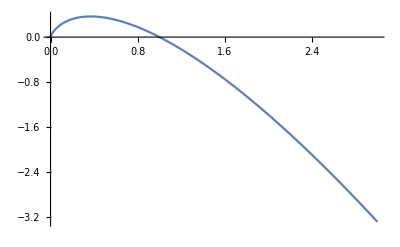

```mathematica
Plot[x Log[1/x],{x,0,3}]
```

```mathematica
Integrate[1 /(k(k^2+1)^(1/2)),{k,0,b}]
```

Integrate::idiv: Integral of 1/(k √(1+k^2)) does not converge on {0,b}.

∫_0^b 1/(k √(1+k^2))ⅆk

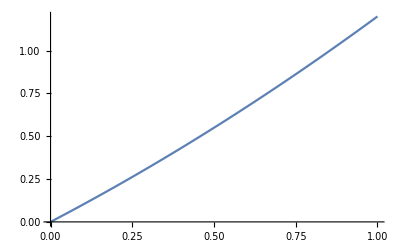

```mathematica
Plot[x+0.2 x^2,{x,0,1}]
```

```mathematica
Integrate[x/(x^2+1)^(1/2),{x,0,a}]
```

-1+√(1+a^2)

```mathematica
Integrate[x/((x^2+1)^(1/2)+b),{x,0,a}]
```

ConditionalExpression[-1+√(1+a^2)+b Log[1+b]-b Log[√(1+a^2)+b],Re[b]≥-1&&Re[√(1+a^2)+b]≥0&&(Re[b+√(1+(a^2 (1+Im[b]^2))/Im[a]^2)]≥0||((√(1+Im[b]^2))/Abs[Im[a]]≥1&&a∉Reals&&(Abs[Im[a]]≤1||√(-1+Im[a]^2)≤Im[b]||√(-1+Im[a]^2)+Im[b]≤0))||a∈Reals)]

```mathematica
Integrate[x/(x^2+1)^(3/2),{x,0,a}]
```

1-1/(√(1+a^2))

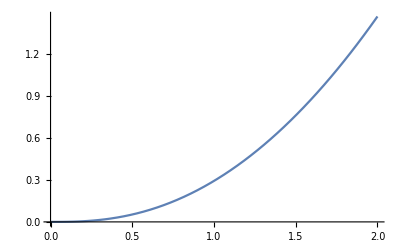

```mathematica
Plot[delta^3(1-1/(1+1/delta)^(1/2)),{delta,0,2}]
```

### a two band model by iskin

```mathematica
h0[t_,kx_,ky_]:=2t-t(kx^2+ky^2);
hx[t_,kx_,ky_]:=-t(kx^2-ky^2);
hz[t_,kx_,ky_]:=-2t kx ky;
```

```mathematica
sigma0={{1,0},{0,1}};
sigmax={{0,1},{1,0}};
sigmay={{0,-I},{I,0}};
sigmaz={{1,0},{0,-1}};
```

```mathematica
Eigenvalues[h0[t,kx,ky]sigma0+hx[t,kx,ky]sigmax+hz[t,kx,ky]sigmaz]
```

{2 t,-2 (-1+kx^2+ky^2) t}

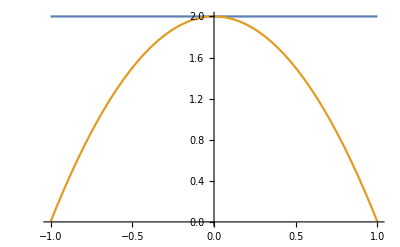

```mathematica
t=1;
Plot[{2t,-2(-1+kx^2)t},{kx,-1,1}]
```

```mathematica
Integrate[(1/x)-(1/x)(1/Sqrt[x^4+1]),{x,0,a}]
```

1/2 Log[1/2 (1+√(1+a^4))]

```mathematica
Integrate[(1/x)-(1/x)(1/Sqrt[x^2+1]),{x,0,a}]
```

Log[1/2 (1+√(1+a^2))]

### massive iskin’s model

```mathematica
Clear[t,m]
Eigenvalues[h0[t,kx,ky]sigma0+hx[t,kx,ky]sigmax+(hz[t,kx,ky])sigmay+m sigmaz]
```

{2 t-kx^2 t-ky^2 t-√(m^2+kx^4 t^2+2 kx^2 ky^2 t^2+ky^4 t^2),2 t-kx^2 t-ky^2 t+√(m^2+kx^4 t^2+2 kx^2 ky^2 t^2+ky^4 t^2)}

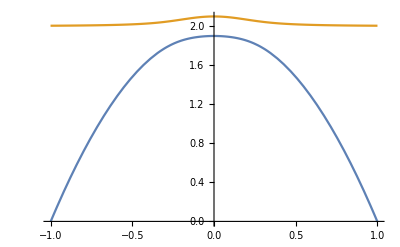

```mathematica
t=1;m=0.1;
Plot[{2 t-kx^2 t-√(m^2+kx^4 t^2),2 t-kx^2 t+√(m^2+kx^4 t^2)},{kx,-1,1}]
```

```mathematica
Clear[t,m]
```

```mathematica
dx[m_,kx_,ky_]:=-t(kx^2-ky^2)/Sqrt[m^2+t^2(kx^2+ky^2)^2]
```

```mathematica
dy[m_,kx_,ky_]:=-2t kx ky/Sqrt[m^2+t^2(kx^2+ky^2)^2]
```

```mathematica
dz[m_,kx_,ky_]:=m/Sqrt[m^2+t^2(kx^2+ky^2)^2]
```

```mathematica
FullSimplify[D[dx[m,kx,ky],kx]D[dx[m,kx,ky],kx]+D[dy[m,kx,ky],kx]D[dy[m,kx,ky],kx]+D[dz[m,kx,ky],kx]D[dz[m,kx,ky],kx]]
```

(4 (kx^2+ky^2) t^2 (m^2+ky^2 (kx^2+ky^2) t^2))/((m^2+(kx^2+ky^2)^2 t^2)^2)

```mathematica
FullSimplify[D[dx[m,kx,ky],kx]D[dx[m,kx,ky],ky]+D[dy[m,kx,ky],kx]D[dy[m,kx,ky],ky]+D[dz[m,kx,ky],kx]D[dz[m,kx,ky],ky]]
```

-(4 kx ky (kx^2+ky^2)^2 t^4)/((m^2+(kx^2+ky^2)^2 t^2)^2)

### Mielke dispersion plot

```mathematica
d0is[t_,t1_,t2_,kx_,ky_]:=-2(t1+t2)Cos[kx]Cos[ky]
```

```mathematica
dxis[t_,t1_,t2_,kx_,ky_]:=-2t Cos[kx]-2t Cos[ky]
```

```mathematica
dzis[t_,t1_,t2_,kx_,ky_]:=2(t1-t2)Sin[kx]Sin[ky]
```

```mathematica
Eigenvalues[d0is[t,t1,t2,kx,ky]sigma0+dxis[t,t1,t2,kx,ky]sigmax+dzis[t,t1,t2,kx,ky]sigmaz]
```

{1/2 (-2 t1 Cos[kx-ky]-2 t2 Cos[kx-ky]-2 t1 Cos[kx+ky]-2 t2 Cos[kx+ky]-√((2 t1 Cos[kx-ky]+2 t2 Cos[kx-ky]+2 t1 Cos[kx+ky]+2 t2 Cos[kx+ky])^2-8 (-2 t^2+2 t1 t2-t^2 Cos[2 kx]+t1^2 Cos[2 kx]+t2^2 Cos[2 kx]+t1 t2 Cos[2 kx-2 ky]-2 t^2 Cos[kx-ky]-t^2 Cos[2 ky]+t1^2 Cos[2 ky]+t2^2 Cos[2 ky]-2 t^2 Cos[kx+ky]+t1 t2 Cos[2 kx+2 ky]))),1/2 (-2 t1 Cos[kx-ky]-2 t2 Cos[kx-ky]-2 t1 Cos[kx+ky]-2 t2 Cos[kx+ky]+√((2 t1 Cos[kx-ky]+2 t2 Cos[kx-ky]+2 t1 Cos[kx+ky]+2 t2 Cos[kx+ky])^2-8 (-2 t^2+2 t1 t2-t^2 Cos[2 kx]+t1^2 Cos[2 kx]+t2^2 Cos[2 kx]+t1 t2 Cos[2 kx-2 ky]-2 t^2 Cos[kx-ky]-t^2 Cos[2 ky]+t1^2 Cos[2 ky]+t2^2 Cos[2 ky]-2 t^2 Cos[kx+ky]+t1 t2 Cos[2 kx+2 ky])))}

```mathematica
t=1;t1=1;t2=0;
Plot3D[{1/2 (-2 t1 Cos[kx-ky]-2 t2 Cos[kx-ky]-2 t1 Cos[kx+ky]-2 t2 Cos[kx+ky]-√((2 t1 Cos[kx-ky]+2 t2 Cos[kx-ky]+2 t1 Cos[kx+ky]+2 t2 Cos[kx+ky])^2-8 (-2 t^2+2 t1 t2-t^2 Cos[2 kx]+t1^2 Cos[2 kx]+t2^2 Cos[2 kx]+t1 t2 Cos[2 kx-2 ky]-2 t^2 Cos[kx-ky]-t^2 Cos[2 ky]+t1^2 Cos[2 ky]+t2^2 Cos[2 ky]-2 t^2 Cos[kx+ky]+t1 t2 Cos[2 kx+2 ky]))),1/2 (-2 t1 Cos[kx-ky]-2 t2 Cos[kx-ky]-2 t1 Cos[kx+ky]-2 t2 Cos[kx+ky]+√((2 t1 Cos[kx-ky]+2 t2 Cos[kx-ky]+2 t1 Cos[kx+ky]+2 t2 Cos[kx+ky])^2-8 (-2 t^2+2 t1 t2-t^2 Cos[2 kx]+t1^2 Cos[2 kx]+t2^2 Cos[2 kx]+t1 t2 Cos[2 kx-2 ky]-2 t^2 Cos[kx-ky]-t^2 Cos[2 ky]+t1^2 Cos[2 ky]+t2^2 Cos[2 ky]-2 t^2 Cos[kx+ky]+t1 t2 Cos[2 kx+2 ky])))},{kx,-π,π},{ky,-π,π}]
```

-Graphics3D-

```mathematica
Eigenvalues[d0is[t,t1,t2,kx,ky]sigma0+dxis[t,t1,t2,kx,ky]sigmax+dzis[t,t1,t2,kx,ky]sigmay+m sigmaz]
```

{1/2 (-2 Cos[kx-ky]-2 Cos[kx+ky]-√(-4 (-4-m^2-4 Cos[kx-ky]-4 Cos[kx+ky])+(2 Cos[kx-ky]+2 Cos[kx+ky])^2)),1/2 (-2 Cos[kx-ky]-2 Cos[kx+ky]+√(-4 (-4-m^2-4 Cos[kx-ky]-4 Cos[kx+ky])+(2 Cos[kx-ky]+2 Cos[kx+ky])^2))}

```mathematica
Plot3D[{1/2 (-2 Cos[kx-ky]-2 Cos[kx+ky]-√(-4 (-4-m^2-4 Cos[kx-ky]-4 Cos[kx+ky])+(2 Cos[kx-ky]+2 Cos[kx+ky])^2)),1/2 (-2 Cos[kx-ky]-2 Cos[kx+ky]+√(-4 (-4-m^2-4 Cos[kx-ky]-4 Cos[kx+ky])+(2 Cos[kx-ky]+2 Cos[kx+ky])^2))},{kx,-π,π},{ky,-π,π}]
```

### 2 band model- one flat, the other quadratic

the flat band:

```mathematica
Integrate[x^3(1+x^4/2)/(1+x^4)^2,{x,0,a}]
```

1/8 (a^4/(1+a^4)+Log[1+a^4])

the quadratic band (Ds,2):

```mathematica
Integrate[(1/(1+y)^(1/2))(1/y),y]
```

Log[1-√(1+y)]-Log[1+√(1+y)]

```mathematica
Integrate[(1/(1+y)^(1/2))(1/y^2),y]
```

-(√(1+y))/y+ArcTanh[√(1+y)]

full SW function:

```mathematica
kappap[λ_,delta_]:=2/(Sqrt[1-λ^2]delta);
```

```mathematica
twobandds[λ_,delta_]:=π delta((λ^2 kappap[λ,delta]^2-2)Log[(1+Sqrt[1+λ^2 kappap[λ,delta]^2])/(1+Sqrt[1+ kappap[λ,delta]^2])]+1-λ^2-λ^2 kappap[λ,delta]^2Log[λ]+λ^2Sqrt[1+kappap[λ,delta]^2]-Sqrt[1+λ^2kappap[λ,delta]^2])
```

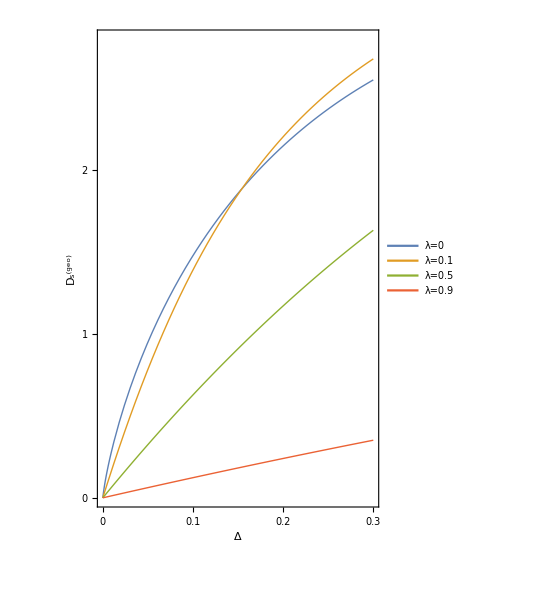

```mathematica
twobandds1=Plot[{twobandds[0.001,delta],twobandds[0.1,delta],twobandds[0.5,delta],twobandds[0.9,delta]},{delta,0,0.3},PlotRange->{{0,0.3},{0,2.8}},
PlotStyle->Directive[Thick],Frame->True,FrameLabel->{"Δ","D_s^(geo)"},RotateLabel->True,LabelStyle->Directive[Black,22],FrameTicks->{{{0,1,2},None},{{0,0.1,0.2,0.3},None}},PlotLegends->Placed[{"λ=0","λ=0.1","λ=0.5","λ=0.9"},{0.23,0.75}],AspectRatio->1.5]
```

```mathematica
Export["twobandds1.png",twobandds1]
```

twobandds1.png

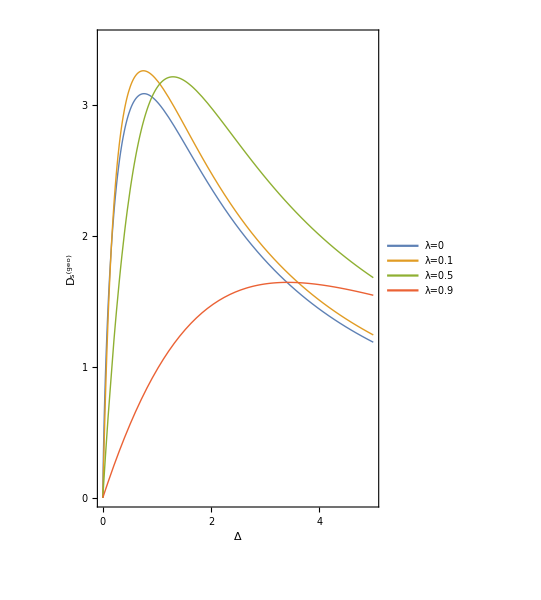

```mathematica
twobandds2=Plot[{twobandds[0.001,delta],twobandds[0.1,delta],twobandds[0.5,delta],twobandds[0.9,delta]},{delta,0,5},PlotRange->{{0,5},{0,3.5}},
PlotStyle->Directive[Thick],Frame->True,FrameLabel->{"Δ","D_s^(geo)"},RotateLabel->True,LabelStyle->Directive[Black,22],FrameTicks->{{{0,1,2,3},None},{{0,1,2,3,4,5},None}},PlotLegends->Placed[{"λ=0","λ=0.1","λ=0.5","λ=0.9"},{0.65,0.23}],AspectRatio->1.5]
```

```mathematica
Export["twobandds2.png",twobandds2]
```

twobandds2.png

```mathematica
twobandslope[λ_]:=π(1-λ^2-2Log[λ])
```

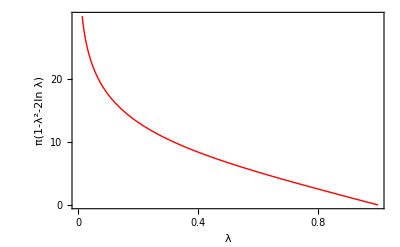

```mathematica
twobandslopeplot=Plot[twobandslope[λ],{λ,0,1},PlotRange->{{0,1},{0,30}},PlotStyle->Directive[Red,Thick],Frame->True,FrameLabel->{"λ","π(1-λ^2-2ln λ)"},RotateLabel->False,LabelStyle->Directive[Black,20],FrameTicks->{{{0,10,20},None},{{0,0.2,0.4,0.6,0.8,1},None}}]
```

```mathematica
Export["twobandslope.png",twobandslopeplot]
```

twobandslope.png

some Taylor expansion below:

```mathematica
Series[Log[(1+Sqrt[1+lambda^2(1/x^2)])/(1+Sqrt[1+(1/x^2)])],{x,0,2}]
```

Log[(1+√(lambda^2/x^2))/(1+√(1/x^2))]+((-lambda^2 √(1/x^2)+√(lambda^2/x^2)+√(1/x^2) √(lambda^2/x^2)-lambda^2 √(1/x^2) √(lambda^2/x^2)) x^2)/(2 lambda^2 (1+√(1/x^2)) (1+√(lambda^2/x^2)))+O[x]^3

```mathematica
Series[((x/lambda)+Sqrt[1+(x/lambda)^2])/(x+Sqrt[1+x^2]),{x,0,3}]
```

1+(-1+1/lambda) x+((1-2 lambda+lambda^2) x^2)/(2 lambda^2)+((-1+lambda) x^3)/(2 lambda^2)+O[x]^4

```mathematica
Series[Log[1+(-1+1/lambda) x+((1-2 lambda+lambda^2) x^2)/(2 lambda^2)],{x,0,3}]
```

(-1+1/lambda) x+((-1+3 lambda-3 lambda^2+lambda^3) x^3)/(6 lambda^3)+O[x]^4

### 2 band model-finite T

```mathematica
Integrate[(1+y)^(-1/2)(1/y),y]
```

Log[1-√(1+y)]-Log[1+√(1+y)]

```mathematica
Integrate[Tanh[(1+y)^(1/2)](1+y)^(-1/2)(1/y),y]
```

∫Tanh[√(1+y)]/(y √(1+y))ⅆy

```mathematica
Integrate[Tanh[(1+y)^(1/2)](1/y),y]
```

∫Tanh[√(1+y)]/y ⅆy

```mathematica
Integrate[Tanh[x],x]
```

Log[Cosh[x]]

```mathematica
Integrate[Tanh[x]/(x^2-a),x]
```

∫Tanh[x]/(-a+x^2)ⅆx

```mathematica
Integrate[Log[x],x]
```

### two band simplify to linear

```mathematica
Series[Log[x+Sqrt[1+x^2]],{x,0,3}]
```

x-x^3/6+O[x]^4

### two bands symmetric, direct integral

```mathematica
Integrate[(1/(x(x-1))^(1/2))(1/((x^(1/2)-(x-1)^(1/2))^2+a)^(1/2)-1/((x^(1/2)+(x-1)^(1/2))^2+a)^(1/2))(x+1)/x,x,Assumptions->Element[a,Positive]]
```

Integrate[((1/(√(a+(-√(-1+x)+√x)^2))-1/(√(a+(√(-1+x)+√x)^2))) (1+x))/(x √((-1+x) x)),x,Assumptions→a∈Positive]

```mathematica
Integrate[(1/(x(x-1))^(1/2))(1/((x^(1/2)-(x-1)^(1/2))^2+a)^(1/2))((x+1)/x),x,Assumptions->Element[a,Positive]]
```

-((2 √((-1+x) x) (2 √a (√(-1+x)-√x) √x √(-1+a-2 √(-1+x) √x+2 x) ArcTanh[(√(-1+a))/(√(-1+a-2 √(-1+x) √x+2 x))]+√(-1+a) (√a (-1+a-2 √(-1+x) √x+2 x)-(-1+a) (√(-1+x)-√x) √x √(-1+a-2 √(-1+x) √x+2 x) ArcTanh[(√a)/(√(-1+a-2 √(-1+x) √x+2 x))])))/((-1+a)^(3/2) √a x (-1-√(-1+x) √x+x) √(-1+a-2 √(-1+x) √x+2 x)))

```mathematica
Integrate[(1/(x(x-1))^(1/2))(1/((x^(1/2)+(x-1)^(1/2))^2+a)^(1/2))(x+1)/x,x,Assumptions->Element[a,Positive]]
```

(2 √((-1+x) x) (-(√(-1+a+2 √(-1+x) √x+2 x))/(-1+a)+(2 (√(-1+x) √x+x) ArcTanh[(√(-1+a))/(√(-1+a+2 √(-1+x) √x+2 x))])/(-1+a)^(3/2)-((√(-1+x) √x+x) ArcTanh[(√a)/(√(-1+a+2 √(-1+x) √x+2 x))])/(√a)))/(x (-1+√(-1+x) √x+x))

```mathematica
Integrate[(1/(z(z+1))^(1/2))(1/(((z+1)^(1/2)-z^(1/2))^2+a)^(1/2))((z+2)/(z+1)),z,Assumptions->Element[a,Positive]]
```

Integrate[(2+z)/((1+z) √(z (1+z)) √(a+(-√z+√(1+z))^2)),z,Assumptions→a∈Positive]

this is funny as when I change the variable by 1 it cannot integrate..

```mathematica
Simplify[-((2 √((-1+x) x) (2 √a (√(-1+x)-√x) √x √(-1+a-2 √(-1+x) √x+2 x) ArcTanh[(√(-1+a))/(√(-1+a-2 √(-1+x) √x+2 x))]+√(-1+a) (√a (-1+a-2 √(-1+x) √x+2 x)-(-1+a) (√(-1+x)-√x) √x √(-1+a-2 √(-1+x) √x+2 x) ArcTanh[(√a)/(√(-1+a-2 √(-1+x) √x+2 x))])))/((-1+a)^(3/2) √a x (-1-√(-1+x) √x+x) √(-1+a-2 √(-1+x) √x+2 x)))-((2 √((-1+x) x) (-(√(-1+a+2 √(-1+x) √x+2 x))/(-1+a)+(2 (√(-1+x) √x+x) ArcTanh[(√(-1+a))/(√(-1+a+2 √(-1+x) √x+2 x))])/(-1+a)^(3/2)-((√(-1+x) √x+x) ArcTanh[(√a)/(√(-1+a+2 √(-1+x) √x+2 x))])/(√a)))/(x (-1+√(-1+x) √x+x))),Assumptions->{Im[a]==0,Im[x]==0,Re[a]>0,Re[x]>1}]
```

1/x 2 √((-1+x) x) (1/(-1+x-√((-1+x) x))((√(-1+a+2 x-2 √((-1+x) x)))/(1-a)-(2 (-x+√((-1+x) x)) ArcTanh[√((-1+a)/(-1+a+2 x-2 √((-1+x) x)))])/(-1+a)^(3/2)+((-√a+√((a (-1+x))/x)) x ArcTanh[√(a/(-1+a+2 x-2 √((-1+x) x)))])/a)-1/(-1+x+√((-1+x) x))((√(-1+a+2 x+2 √((-1+x) x)))/(1-a)+(2 (x+√((-1+x) x)) ArcTanh[√((-1+a)/(-1+a+2 x+2 √((-1+x) x)))])/(-1+a)^(3/2)-((x+√((-1+x) x)) ArcTanh[√(a/(-1+a+2 x+2 √((-1+x) x)))])/(√a)))

```mathematica
finalresult[a_,x_]:=(2/a^(1/2))(ArcTanh[a^(1/2)/(a+(Sqrt[x]-Sqrt[x-1])^2)^(1/2)]+ArcTanh[a^(1/2)/(a+(Sqrt[x]+Sqrt[x-1])^2)^(1/2)])-(4/(a-1)^(3/2))(ArcTanh[(a-1)^(1/2)/(a+(Sqrt[x]-Sqrt[x-1])^2)^(1/2)]+ArcTanh[(a-1)^(1/2)/(a+(Sqrt[x]+Sqrt[x-1])^2)^(1/2)])+(2/(a-1))(1/x^(1/2))(Sqrt[a/(Sqrt[x]-Sqrt[x-1])^2+1]+Sqrt[a/(Sqrt[x]+Sqrt[x-1])^2+1])
```

```mathematica
Simplify[finalresult[a,b+1]-finalresult[a,1]]
```

-(4 √(1+a))/(-1+a)+(2 (√(1+a/(√b-√(1+b))^2)+√(1+a/(√b+√(1+b))^2)))/((-1+a) √(1+b))+(8 ArcTanh[√((-1+a)/(1+a))])/(-1+a)^(3/2)-(4 ArcTanh[√(a/(1+a))])/(√a)-(4 (ArcTanh[(√(-1+a))/(√(a+(√b-√(1+b))^2))]+ArcTanh[(√(-1+a))/(√(a+(√b+√(1+b))^2))]))/(-1+a)^(3/2)+(2 (ArcTanh[(√a)/(√(a+(√b-√(1+b))^2))]+ArcTanh[(√a)/(√(a+(√b+√(1+b))^2))]))/(√a)

```mathematica
netresult[a_,b_]:=-(4 √(1+a))/(-1+a)+(2 (√(1+a/(√b-√(1+b))^2)+√(1+a/(√b+√(1+b))^2)))/((-1+a) √(1+b))+(8 ArcTanh[√((-1+a)/(1+a))])/(-1+a)^(3/2)-(4 ArcTanh[√(a/(1+a))])/(√a)-(4 (ArcTanh[(√(-1+a))/(√(a+(√b-√(1+b))^2))]+ArcTanh[(√(-1+a))/(√(a+(√b+√(1+b))^2))]))/(-1+a)^(3/2)+(2 (ArcTanh[(√a)/(√(a+(√b-√(1+b))^2))]+ArcTanh[(√a)/(√(a+(√b+√(1+b))^2))]))/(√a)
```

```mathematica
N[netresult[1,10]]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

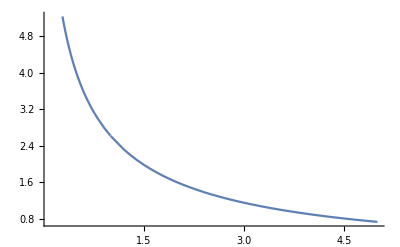

```mathematica
Plot[netresult[a,10],{a,0.1,5}]
```

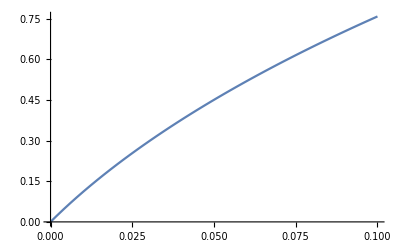

```mathematica
Plot[a netresult[a,10],{a,0,0.1}]
```

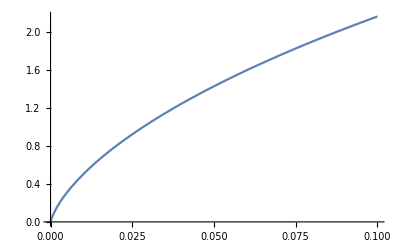

```mathematica
Plot[a netresult[a,1000],{a,0,0.1}]
```

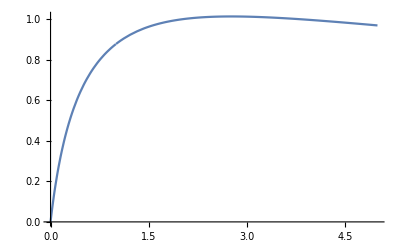

```mathematica
Plot[a netresult[a,1],{a,0,5},PlotRange->Full]
```

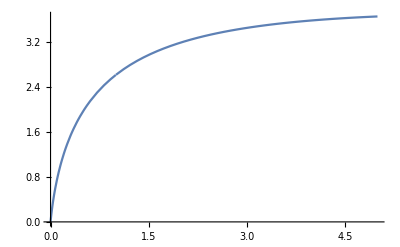

```mathematica
Plot[a netresult[a,10],{a,0,5},PlotRange->Full]
```

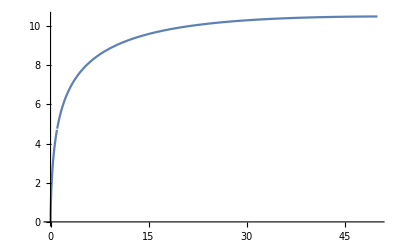

```mathematica
Plot[a netresult[a,100],{a,0,50},PlotRange->Full]
```

### two bands symmetric, cosh sinh integral

```mathematica
ArcCosh[1]
```

0

```mathematica
D[Cosh[x],x]
```

Sinh[x]

```mathematica
Integrate[(1+1/(Cosh[x]^2))(1/((Cosh[x]-Sinh[x])^2+eta)^(1/2)),x,Assumptions->Element[eta,Positive]]
```

$Aborted

the main problme here is eta!!! if choose eta=1 then integrable

```mathematica
Integrate[(1+1/(Cosh[x]^2))(1/((Cosh[x]-Sinh[x])^2+1)^(1/2)),x]
```

(Cosh[x]^(5/2) (1+Sech[x]^2) ((4 (Cosh[x]+Sinh[x]))/(3 Cosh[x]^(3/2))+1/(√(Cosh[x]/(1+Cosh[x])))2 √Cosh[x] (Log[-1+Tanh[x/2]]-Log[1+2 √(Cosh[x]/(1+Cosh[x]))+Tanh[x/2]]) (-1+Tanh[x/2])))/((3+Cosh[2 x]) √(1+(Cosh[x]-Sinh[x])^2))

```mathematica
Integrate[(1+1/(Cosh[x]^2))(1/((Cosh[x]+Sinh[x])^2+1)^(1/2)),x]
```

-((2 (1+Cosh[x]^2) Sech[x] (Cosh[x]+Sinh[x]) (2 Cosh[2 x]-4 Cosh[x] Sinh[x]+3 √2 Cosh[x/2]^2 Cosh[x]^(3/2) (Log[Sech[x/2]^2+√2 √Cosh[x] √(Sech[x/2]^4 (Cosh[x]+Sinh[x]))]-Log[(1+Tanh[x/2])^2]) (Cosh[x]-Sinh[x]) √(Sech[x/2]^4 (Cosh[x]+Sinh[x]))))/(3 (3+Cosh[2 x]) √(1+(Cosh[x]+Sinh[x])^2)))

```mathematica
Integrate[(1+1/(Cosh[x]^2))(1/((Cosh[x]-Sinh[x])^2+1)^(1/2)),x]
```

```mathematica
Integrate[(1/(eta(Cosh[x]-Sinh[x])^2+1)^(1/2)),x,Assumptions->Element[{eta},Positive]]
```

(Cosh[x/2]^2 (Log[1-Tanh[x/2]]+Log[-1+Tanh[x/2]]-2 Log[1+Tanh[x/2]+√(eta (-1+Tanh[x/2])^2+(1+Tanh[x/2])^2)]) (Cosh[x]+Sinh[x]) √(1+eta Cosh[2 x]-eta Sinh[2 x]) (-1+Tanh[x/2]) √(eta (-1+Tanh[x/2])^2+(1+Tanh[x/2])^2))/(2 (1+eta) Cosh[x]-2 (-1+eta) Sinh[x])

```mathematica
Integrate[(1/(Cosh[x]Sinh[x]))(1/((Cosh[x]-Sinh[x])^2+b)^(1/2))Sinh[x]/Cosh[x],x]
```

√(b+Cosh[2 x]-Sinh[2 x]) (1/(-1+b)+((Log[((2+2 ⅈ) (ⅈ+b+√2 √(-1+b) √(((1+b) Cosh[x]+(-1+b) Sinh[x])/(1+Cosh[x]))+(-ⅈ+b) Tanh[x/2]))/(√(-1+b) (ⅈ+Tanh[x/2]))]+Log[((2-2 ⅈ) (-ⅈ+b+√2 √(-1+b) √(((1+b) Cosh[x]+(-1+b) Sinh[x])/(1+Cosh[x]))+(ⅈ+b) Tanh[x/2]))/(√(-1+b) (-ⅈ+Tanh[x/2]))]) √(b Sech[x/2]^4+(-1+Tanh[x/2])^4))/((-1+b)^(3/2) (1+Cosh[x]) √((b+Cosh[2 x]-Sinh[2 x])/(1+Cosh[x])^2) (-1+Tanh[x/2]) √((-1+Tanh[x/2])^2+b (1+Tanh[x/2])^2))+Tanh[x]/(-1+b))

## Lieb lattice calculation

### Lieb lattice

```mathematica
hsimple={{0,a,0},{astar,0,b},{0,bstar,0}};
Eigensystem[hsimple]
```

{{0,-√(a astar+b bstar),√(a astar+b bstar)},{{-b/astar,0,1},{a/bstar,-(√(a astar+b bstar))/bstar,1},{a/bstar,(√(a astar+b bstar))/bstar,1}}}

```mathematica
ak[delta_,kx_,ky_]:=Cos[kx/2]+I delta Sin[kx/2]
```

```mathematica
akstar[delta_,kx_,ky_]:=Cos[kx/2]-I delta Sin[kx/2]
```

```mathematica
bk[delta_,kx_,ky_]:=Cos[ky/2]+I delta Sin[ky/2]
```

```mathematica
bkstar[delta_,kx_,ky_]:=Cos[ky/2]-I delta Sin[ky/2]
```

```mathematica
dispersionlieb[delta_,kx_,ky_]:=(ak[delta,kx,ky]akstar[delta,kx,ky]+bk[delta,kx,ky]bkstar[delta,kx,ky])^(1/2)
```

```mathematica
delta=0;
Plot3D[{dispersionlieb[delta,kx,ky],-dispersionlieb[delta,kx,ky]},{kx,0,2π},{ky,0,2π}]
```

-Graphics3D-

```mathematica
delta=0.2;
Plot3D[{dispersionlieb[delta,kx,ky],-dispersionlieb[delta,kx,ky]},{kx,0,2π},{ky,0,2π}]
```

-Graphics3D-

```mathematica
Clear[delta]
Series[ak[delta,kx,ky]akstar[delta,kx,ky]+bk[delta,kx,ky]bkstar[delta,kx,ky],{kx,π,2},{ky,π,2}]
```

(2 delta^2+(1/4-delta^2/4) (ky-π)^2+O[ky-π]^3)+(1/4-delta^2/4) (kx-π)^2+O[kx-π]^3

### example calculation of qm for two-band model

```mathematica
uc[kx_,ky_]:=1/(2(1-hz[kx,ky]))^(1/2){hx[kx,ky]-I hy[kx,ky],1-hz[kx,ky]};
ucstar[kx_,ky_]:=1/(2(1-hz[kx,ky]))^(1/2){hx[kx,ky]+I hy[kx,ky],1-hz[kx,ky]};
uv[kx_,ky_]:=1/(2(1+hz[kx,ky]))^(1/2){-(hx[kx,ky]-I hy[kx,ky]),1+hz[kx,ky]};
uvstar[kx_,ky_]:=1/(2(1+hz[kx,ky]))^(1/2){-(hx[kx,ky]+I hy[kx,ky]),1+hz[kx,ky]};
```

```mathematica
FullSimplify[(-(D[ucstar[kx,ky],ky].uv[kx,ky])(uvstar[kx,ky].D[uc[kx,ky],ky])-(uvstar[kx,ky].D[uc[kx,ky],ky])(D[ucstar[kx,ky],ky].uv[kx,ky]))/2]
```

(4 (hx[kx,ky]^2+hy[kx,ky]^2) (-1+hz[kx,ky])^2 ((hx^(0,1)[kx,ky])^2+(hy^(0,1)[kx,ky])^2)-4 (-1+hz[kx,ky]) (1+hx[kx,ky]^2+hy[kx,ky]^2-hz[kx,ky]^2) (hx[kx,ky] hx^(0,1)[kx,ky]+hy[kx,ky] hy^(0,1)[kx,ky]) hz^(0,1)[kx,ky]+(1+hx[kx,ky]^2+hy[kx,ky]^2-hz[kx,ky]^2)^2 (hz^(0,1)[kx,ky])^2)/(16 (-1+hz[kx,ky])^3 (1+hz[kx,ky]))

```mathematica
Simplify[(4 (1-hz[kx,ky]^2) (-1+hz[kx,ky])^2 ((Derivative[0,1][hx][kx,ky])^2+(Derivative[0,1][hy][kx,ky])^2)-4 (-1+hz[kx,ky]) (2-2 hz[kx,ky]^2) (hx[kx,ky] Derivative[0,1][hx][kx,ky]+hy[kx,ky] Derivative[0,1][hy][kx,ky]) Derivative[0,1][hz][kx,ky]+(2-2 hz[kx,ky]^2)^2 (Derivative[0,1][hz][kx,ky])^2)/(16 (-1+hz[kx,ky])^3 (1+hz[kx,ky]))]
```

1/(4 (-1+hz[kx,ky]))(-(-1+hz[kx,ky]) (hx^(0,1)[kx,ky])^2-(-1+hz[kx,ky]) (hy^(0,1)[kx,ky])^2+2 hx[kx,ky] hx^(0,1)[kx,ky] hz^(0,1)[kx,ky]+2 hy[kx,ky] hy^(0,1)[kx,ky] hz^(0,1)[kx,ky]+(1+hz[kx,ky]) (hz^(0,1)[kx,ky])^2)

### compute the quantum metric

```mathematica
u0k=(1/(a[kx,ky]astar[kx,ky]+b[kx,ky]bstar[kx,ky])^(1/2)){-b[kx,ky],0,astar[kx,ky]};
u0kstar=(1/(a[kx,ky]astar[kx,ky]+b[kx,ky]bstar[kx,ky])^(1/2)){-bstar[kx,ky],0,a[kx,ky]};
upk=(1/Sqrt[2]){a[kx,ky]/(a[kx,ky]astar[kx,ky]+b[kx,ky]bstar[kx,ky])^(1/2),1,bstar[kx,ky]/(a[kx,ky]astar[kx,ky]+b[kx,ky]bstar[kx,ky])^(1/2)};
upkstar=(1/Sqrt[2]){astar[kx,ky]/(a[kx,ky]astar[kx,ky]+b[kx,ky]bstar[kx,ky])^(1/2),1,b[kx,ky]/(a[kx,ky]astar[kx,ky]+b[kx,ky]bstar[kx,ky])^(1/2)};
umk=(1/Sqrt[2]){a[kx,ky]/(a[kx,ky]astar[kx,ky]+b[kx,ky]bstar[kx,ky])^(1/2),-1,bstar[kx,ky]/(a[kx,ky]astar[kx,ky]+b[kx,ky]bstar[kx,ky])^(1/2)};
umkstar=(1/Sqrt[2]){astar[kx,ky]/(a[kx,ky]astar[kx,ky]+b[kx,ky]bstar[kx,ky])^(1/2),-1,b[kx,ky]/(a[kx,ky]astar[kx,ky]+b[kx,ky]bstar[kx,ky])^(1/2)};
```

R^(0,+):

```mathematica
Simplify[-(D[u0kstar,kx].upk)(upkstar.D[u0k,ky])]
```

-(((-b[kx,ky] astar^(0,1)[kx,ky]+astar[kx,ky] b^(0,1)[kx,ky]) (-bstar[kx,ky] a^(1,0)[kx,ky]+a[kx,ky] bstar^(1,0)[kx,ky]))/(2 (a[kx,ky] astar[kx,ky]+b[kx,ky] bstar[kx,ky])^2))

g^(0,+):

```mathematica
Simplify[(-(D[u0kstar,kx].upk)(upkstar.D[u0k,ky])-(upkstar.D[u0k,kx])(D[u0kstar,ky].upk))/2]
```

(b[kx,ky] (-bstar[kx,ky] (astar^(0,1)[kx,ky] a^(1,0)[kx,ky]+a^(0,1)[kx,ky] astar^(1,0)[kx,ky])+a[kx,ky] (bstar^(0,1)[kx,ky] astar^(1,0)[kx,ky]+astar^(0,1)[kx,ky] bstar^(1,0)[kx,ky]))+astar[kx,ky] (bstar[kx,ky] (b^(0,1)[kx,ky] a^(1,0)[kx,ky]+a^(0,1)[kx,ky] b^(1,0)[kx,ky])-a[kx,ky] (bstar^(0,1)[kx,ky] b^(1,0)[kx,ky]+b^(0,1)[kx,ky] bstar^(1,0)[kx,ky])))/(4 (a[kx,ky] astar[kx,ky]+b[kx,ky] bstar[kx,ky])^2)

direct applying the model functions:

```mathematica
u0[delta_,kx_,ky_]:=(1/(ak[delta,kx,ky]akstar[delta,kx,ky]+bk[delta,kx,ky]bkstar[delta,kx,ky])^(1/2)){-bk[delta,kx,ky],0,akstar[delta,kx,ky]};
u0star[delta_,kx_,ky_]:=(1/(ak[delta,kx,ky]akstar[delta,kx,ky]+bk[delta,kx,ky]bkstar[delta,kx,ky])^(1/2)){-bkstar[delta,kx,ky],0,ak[delta,kx,ky]};
up[delta_,kx_,ky_]:=(1/Sqrt[2]){ak[delta,kx,ky]/(ak[delta,kx,ky]akstar[delta,kx,ky]+bk[delta,kx,ky]bkstar[delta,kx,ky])^(1/2),1,bkstar[delta,kx,ky]/(ak[delta,kx,ky]akstar[delta,kx,ky]+bk[delta,kx,ky]bkstar[delta,kx,ky])^(1/2)};
upstar[delta_,kx_,ky_]:=(1/Sqrt[2]){akstar[delta,kx,ky]/(ak[delta,kx,ky]akstar[delta,kx,ky]+bk[delta,kx,ky]bkstar[delta,kx,ky])^(1/2),1,bk[delta,kx,ky]/(ak[delta,kx,ky]akstar[delta,kx,ky]+bk[delta,kx,ky]bkstar[delta,kx,ky])^(1/2)};
um[delta_,kx_,ky_]:=(1/Sqrt[2]){ak[delta,kx,ky]/(ak[delta,kx,ky]akstar[delta,kx,ky]+bk[delta,kx,ky]bkstar[delta,kx,ky])^(1/2),-1,bkstar[delta,kx,ky]/(ak[delta,kx,ky]akstar[delta,kx,ky]+bk[delta,kx,ky]bkstar[delta,kx,ky])^(1/2)};
umstar[delta_,kx_,ky_]:=(1/Sqrt[2]){akstar[delta,kx,ky]/(ak[delta,kx,ky]akstar[delta,kx,ky]+bk[delta,kx,ky]bkstar[delta,kx,ky])^(1/2),-1,bk[delta,kx,ky]/(ak[delta,kx,ky]akstar[delta,kx,ky]+bk[delta,kx,ky]bkstar[delta,kx,ky])^(1/2)};
```

g^(0,+), xx

```mathematica
FullSimplify[(-(D[u0star[delta,kx,ky],kx].up[delta,kx,ky])(upstar[delta,kx,ky].D[u0[delta,kx,ky],kx])-(upstar[delta,kx,ky].D[u0[delta,kx,ky],kx])(D[u0star[delta,kx,ky],kx].up[delta,kx,ky]))/2]
```

((1+delta^2+(-1+delta^2) Cos[kx]) (-1-delta^2+(-1+delta^2) Cos[ky]))/(8 (2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky])^2)

```mathematica
Series[2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky],{kx,π,2},{ky,π,2}]
```

(4 delta^2+(1/2-delta^2/2) (ky-π)^2+O[ky-π]^3)+(1/2-delta^2/2) (kx-π)^2+O[kx-π]^3

```mathematica
Series[(1+delta^2+(-1+delta^2) Cos[kx]) (-1-delta^2+(-1+delta^2) Cos[ky]),{kx,π,2},{ky,π,2}]
```

(-4 delta^2+(-1+delta^2) (ky-π)^2+O[ky-π]^3)+((delta^2-delta^4)+(1/4-delta^2/2+delta^4/4) (ky-π)^2+O[ky-π]^3) (kx-π)^2+O[kx-π]^3

yy

```mathematica
FullSimplify[(-(D[u0star[delta,kx,ky],ky].up[delta,kx,ky])(upstar[delta,kx,ky].D[u0[delta,kx,ky],ky])-(upstar[delta,kx,ky].D[u0[delta,kx,ky],ky])(D[u0star[delta,kx,ky],ky].up[delta,kx,ky]))/2]
```

((-1-delta^2+(-1+delta^2) Cos[kx]) (1+delta^2+(-1+delta^2) Cos[ky]))/(8 (2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky])^2)

xy

```mathematica
FullSimplify[(-(D[u0star[delta,kx,ky],kx].up[delta,kx,ky])(upstar[delta,kx,ky].D[u0[delta,kx,ky],ky])-(upstar[delta,kx,ky].D[u0[delta,kx,ky],kx])(D[u0star[delta,kx,ky],ky].up[delta,kx,ky]))/2]
```

(-4 delta^2+(-1+delta^2)^2 Sin[kx] Sin[ky])/(8 (2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky])^2)

```mathematica
Series[-4 delta^2+(-1+delta^2)^2 Sin[kx] Sin[ky],{kx,π,2},{ky,π,2}]
```

-4 delta^2+((1-2 delta^2+delta^4) (ky-π)+O[ky-π]^3) (kx-π)+O[kx-π]^3

check positive definiteness:

```mathematica
matrix={{4delta^2+(1-delta^2)ky^2-delta^2(1-delta^2)kx^2,4delta^2-(1-delta^2)^2kx ky},{4delta^2-(1-delta^2)^2kx ky,4delta^2+(1-delta^2)kx^2-delta^2(1-delta^2)ky^2}};
```

```mathematica
Simplify[Tr[matrix]]
```

kx^2+ky^2-2 delta^2 (-4+kx^2+ky^2)+delta^4 (kx^2+ky^2)

```mathematica
Simplify[Det[matrix]]
```

-delta^2 (-1+delta^2)^2 (kx+ky)^2 (-4+kx^2-2 kx ky+ky^2)

```mathematica
smatrix={{(1+delta^2+(-1+delta^2) Cos[kx]) (-1-delta^2+(-1+delta^2) Cos[ky]),-4 delta^2+(-1+delta^2)^2 Sin[kx] Sin[ky]},{-4 delta^2+(-1+delta^2)^2 Sin[kx] Sin[ky],(1+delta^2+(-1+delta^2) Cos[ky]) (-1-delta^2+(-1+delta^2) Cos[kx])}};
```

```mathematica
Simplify[Tr[smatrix]]
```

2 (-(1+delta^2)^2+(-1+delta^2)^2 Cos[kx] Cos[ky])

```mathematica
Simplify[Det[smatrix]]
```

4 delta^2 (-1+delta^2)^2 (Sin[kx]+Sin[ky])^2

g^(0,-), xx

```mathematica
FullSimplify[(-(D[u0star[delta,kx,ky],kx].um[delta,kx,ky])(umstar[delta,kx,ky].D[u0[delta,kx,ky],kx])-(umstar[delta,kx,ky].D[u0[delta,kx,ky],kx])(D[u0star[delta,kx,ky],kx].um[delta,kx,ky]))/2]
```

((1+delta^2+(-1+delta^2) Cos[kx]) (-1-delta^2+(-1+delta^2) Cos[ky]))/(8 (2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky])^2)

yy

```mathematica
FullSimplify[(-(D[u0star[delta,kx,ky],ky].um[delta,kx,ky])(umstar[delta,kx,ky].D[u0[delta,kx,ky],ky])-(umstar[delta,kx,ky].D[u0[delta,kx,ky],ky])(D[u0star[delta,kx,ky],ky].um[delta,kx,ky]))/2]
```

((-1-delta^2+(-1+delta^2) Cos[kx]) (1+delta^2+(-1+delta^2) Cos[ky]))/(8 (2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky])^2)

xy

```mathematica
FullSimplify[(-(D[u0star[delta,kx,ky],kx].um[delta,kx,ky])(umstar[delta,kx,ky].D[u0[delta,kx,ky],ky])-(umstar[delta,kx,ky].D[u0[delta,kx,ky],kx])(D[u0star[delta,kx,ky],ky].um[delta,kx,ky]))/2]
```

(-4 delta^2+(-1+delta^2)^2 Sin[kx] Sin[ky])/(8 (2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky])^2)

g^(+,-), xx

```mathematica
FullSimplify[(-(D[upstar[delta,kx,ky],kx].um[delta,kx,ky])(umstar[delta,kx,ky].D[up[delta,kx,ky],kx])-(umstar[delta,kx,ky].D[up[delta,kx,ky],kx])(D[upstar[delta,kx,ky],kx].um[delta,kx,ky]))/2]
```

-(delta^2/(4 (2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky])^2))

yy

```mathematica
FullSimplify[(-(D[upstar[delta,kx,ky],ky].um[delta,kx,ky])(umstar[delta,kx,ky].D[up[delta,kx,ky],ky])-(umstar[delta,kx,ky].D[up[delta,kx,ky],ky])(D[upstar[delta,kx,ky],ky].um[delta,kx,ky]))/2]
```

-(delta^2/(4 (2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky])^2))

xy

```mathematica
FullSimplify[(-(D[upstar[delta,kx,ky],kx].um[delta,kx,ky])(umstar[delta,kx,ky].D[up[delta,kx,ky],ky])-(umstar[delta,kx,ky].D[up[delta,kx,ky],kx])(D[upstar[delta,kx,ky],ky].um[delta,kx,ky]))/2]
```

delta^2/(4 (2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky])^2)

```mathematica
Series[2+2 delta^2+Cos[kx]-delta^2 Cos[kx]+Cos[ky]-delta^2 Cos[ky],{kx,π,2},{ky,π,2}]
```

(4 delta^2+(1/2-delta^2/2) (ky-π)^2+O[ky-π]^3)+(1/2-delta^2/2) (kx-π)^2+O[kx-π]^3

### Lieb lattice: integral

two integrals for D(0,+):

```mathematica
Integrate[(1/y)(1-1/Sqrt[1+y]),y,Assumptions->Element[{delta,a},Positive]]
```

2 Log[1+√(1+y)]

```mathematica
Integrate[(1/y^2)(1-1/Sqrt[1+y]),y,Assumptions->Element[{delta,a},Positive]]
```

(1+y-√(1+y))/(y √(1+y))-ArcTanh[√(1+y)]

two integrals for D(+,-):

```mathematica
Integrate[(1/x^2)(1/Sqrt[1+x]-1/(1+x)^(3/2)),x,Assumptions->Element[{delta,a},Positive]]
```

2/(√(1+x))+Log[1-√(1+x)]-Log[1+√(1+x)]

## Taylor expansions

### two band model

```mathematica
(*geometric term*)
```

```mathematica
Series[Log[Sqrt[1+x^2]+x],{x,0,3}]
```

x-x^3/6+O[x]^4

```mathematica
Series[(2-lambda^2/x^2)(-Log[lambda]+x-x^3/6-x/lambda+x^3/(6lambda^3))+1-lambda^2-lambda^2Log[lambda]/x^2-(lambda/x)(1+x^2/lambda^2)^(1/2)+(lambda^2/x)(1+x^2)^(1/2),{x,0,2}]
```

(1-lambda^2-2 Log[lambda])+(2 (-4+3 lambda+lambda^3) x)/(3 lambda)+O[x]^3

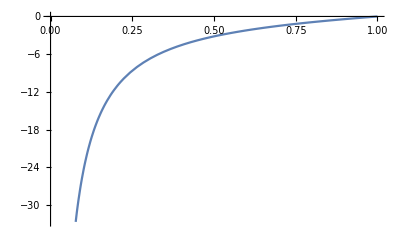

```mathematica
(*quadratic term of geometric part is always negative*)
Plot[2lambda^2/3+2-8/(3lambda),{lambda,0,1}]
```

```mathematica
(*conventional term*)
```

```mathematica
Series[(lambda^2/x^2)(-Log[lambda]+x-x^3/6-x/lambda+x^3/(6lambda^3))+lambda^2Log[lambda]/x^2+(lambda/x)(1+x^2/lambda^2)^(1/2)-(1+lambda^2/x^2)x(1+x^2)^(-1/2),{x,0,2}]
```

((2-3 lambda+lambda^3) x)/(3 lambda)+O[x]^3

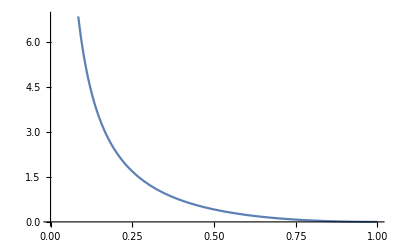

```mathematica
(*quadratic term of conv part*)
Plot[lambda^2/3-1+2/(3lambda),{lambda,0,1}]
```

### dirac model

```mathematica
(*geo part*)
Series[((1+lambda)/(1-lambda))(-Log[lambda]+x-x^3/6-x/lambda+x^3/(6lambda^3)),{x,0,2}]
```

((1+lambda) Log[lambda])/(-1+lambda)+((-1-lambda) x)/lambda+O[x]^3

```mathematica
(*geo part*)
Series[2-x/(1+x^2)^(1/2)-(x/lambda)/(1+x^2/lambda^2)^(1/2),{x,0,2}]
```

2+(-1-1/lambda) x+O[x]^3

### lieb lattice

```mathematica
Integrate[k/(1+a k^2)^2,k]
```

-1/(2 a (1+a k^2))

```mathematica
(*conv term integral*)
```

```mathematica
Integrate[(1+x)^(-3/2),x]
```

-2/(√(1+x))

```mathematica
Integrate[(1/x)(1+x)^(-3/2),x]
```

2/(√(1+x))+Log[1-√(1+x)]-Log[1+√(1+x)]

## Function and D_s^α plots

### 2 band model- one flat, the other J power

plot two bands:

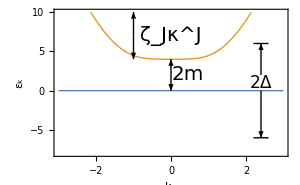

```mathematica
m=2;
energyscale=Plot[{0,2(k^4+m^2)^(1/2)},{k,-3,3},PlotRange->{{-3,3},{-8,10}},Axes->False,
PlotStyle->Directive[Thick],Frame->True,FrameLabel->{Style["k_x",20],Style["ε_k",25]},FrameStyle->Directive[Thickness[0.007]],FrameTicks->{{None,None},{None,None}},RotateLabel->False,LabelStyle->Directive[Black,22],(*AspectRatio->0.7,*)Epilog->{Black,Arrowheads[0.05],Arrow[{{0,2},{0,4}}],Arrow[{{0,2},{0,0}}],Text[Style["2m",Italic,20],{0.45,2}],Arrow[{{-1,7},{-1,10}}],Arrow[{{-1,7},{-1,4}}],Text[Style["ζ_Jκ^J",20],{0,7}],Line[{{2.2,6},{2.6,6}}],Line[{{2.2,-6},{2.6,-6}}],Arrowheads[0.05],Arrow[{{2.4,2},{2.4,6}}],Arrow[{{2.4,0},{2.4,-6}}],Text[Style["2Δ",17],{2.4,1}]},ImageSize->300]
```

```mathematica
Export["energyscale.pdf",energyscale]
```

energyscale.pdf

```mathematica
twobandconvcoeff[λ_]:=(1/(4π))(λ^2/3-1+2/(3λ))
twobandgeocoeff[λ_]:=(1/(8π))(1-λ^2-2Log[λ])
```

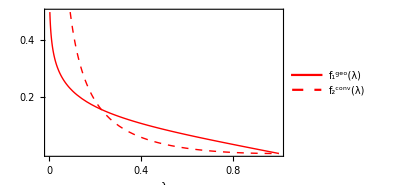

```mathematica
twobandcoeffplot=Plot[{twobandgeocoeff[λ],twobandconvcoeff[λ]},{λ,0,1},PlotRange->{{0,1},{0,0.5}},PlotStyle->{Directive[Red,Thick],Directive[Red,Thick,Dashed]},Frame->True,FrameLabel->{"λ",None},RotateLabel->False,LabelStyle->Directive[Black,20],FrameTicks->{{{0.2,0.4},None},{{0,0.2,0.4,0.6,0.8,1},None}},
FrameStyle->Directive[Thickness[0.007]],PlotLegends->Placed[LineLegend[{Style["f_1^geo(λ)",20],Style["f_2^conv(λ)",20]},LegendLayout->{"Row",2}],{0.7,0.7}],ImageSize->300]
```

```mathematica
Export["twobandcoeff.pdf",twobandcoeffplot]
```

twobandcoeff.pdf

full SW function:

```mathematica
kappap[λ_,delta_]:=2/(Sqrt[1-λ^2]delta);
chi[λ_,delta_]:=Log[(1+Sqrt[1+kappap[λ,delta]^2])/(1+Sqrt[1+λ^2 kappap[λ,delta]^2])]
```

```mathematica
twobandgeods[λ_,delta_]:=(1/(8π)) delta((2-λ^2 kappap[λ,delta]^2)chi[λ,delta]+1-λ^2-λ^2 kappap[λ,delta]^2Log[λ]+λ^2Sqrt[1+kappap[λ,delta]^2]-Sqrt[1+λ^2kappap[λ,delta]^2])
```

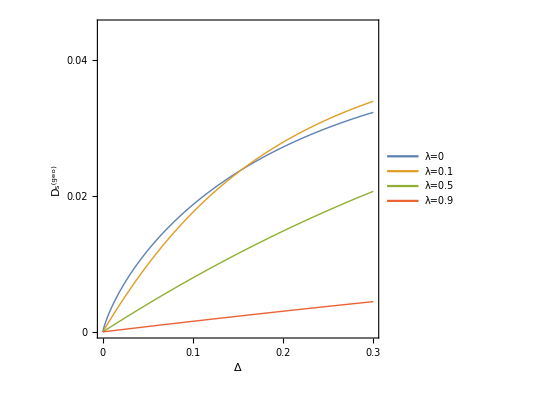

```mathematica
twobandds1=Plot[{twobandds[0.00001,delta],twobandds[0.1,delta],twobandds[0.5,delta],twobandds[0.9,delta]},{delta,0,0.3},PlotRange->{{0,0.3},{0,0.045}},
PlotStyle->Directive[Thick],Frame->True,FrameLabel->{"Δ","D_s^(geo)"},RotateLabel->False,LabelStyle->Directive[Black,22],FrameTicks->{{{0,0.02,0.04},None},{{0,0.1,0.2,0.3},None}},
FrameStyle->Directive[Thickness[0.007]],PlotLegends->Placed[LineLegend[{Style["λ=0",20],Style["λ=0.1",20],Style["λ=0.5",20],Style["λ=0.9",20]},LegendLayout->{"Row",2}],{0.45,0.82}],AspectRatio->1]
```

```mathematica
Export["twobandds1.pdf",twobandds1]
```

twobandds1.pdf

```mathematica
(*still fix kappa to be 1*)
```

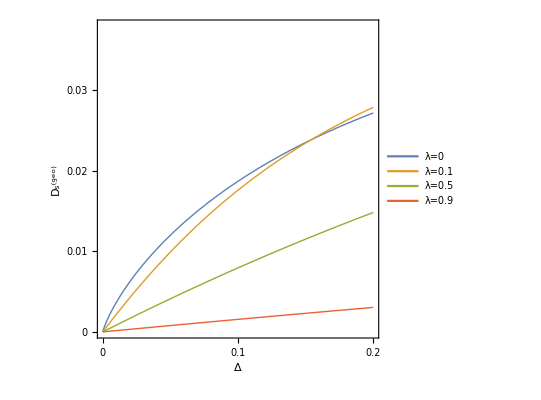

```mathematica
twobandds1=Plot[{twobandds[0.00001,delta],twobandds[0.1,delta],twobandds[0.5,delta],twobandds[0.9,delta]},{delta,0,0.2},PlotRange->{{0,0.2},{0,0.038}},
PlotStyle->Directive[Thick],Frame->True,FrameLabel->{"Δ","D_s^(geo)"},RotateLabel->False,LabelStyle->Directive[Black,22],FrameTicks->{{{0,0.01,0.02,0.03},None},{{0,0.1,0.2},None}},
FrameStyle->Directive[Thickness[0.007]],PlotLegends->Placed[LineLegend[{Style["λ=0",20],Style["λ=0.1",20],Style["λ=0.5",20],Style["λ=0.9",20]},LegendLayout->{"Row",2}],{0.45,0.82}],AspectRatio->1]
```

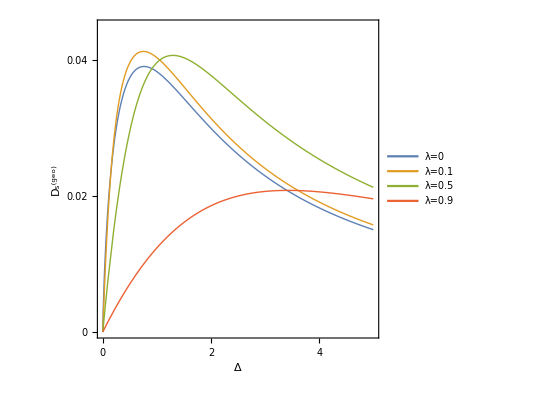

```mathematica
twobandds2=Plot[{twobandds[0.00001,delta],twobandds[0.1,delta],twobandds[0.5,delta],twobandds[0.9,delta]},{delta,0,5},PlotRange->{{0,5},{0,0.045}},
PlotStyle->Directive[Thick],Frame->True,FrameLabel->{"Δ","D_s^(geo)"},RotateLabel->False,LabelStyle->Directive[Black,22],FrameTicks->{{{0,0.02,0.04},None},{{0,1,2,3,4,5},None}},
FrameStyle->Directive[Thickness[0.007]],PlotLegends->Placed[LineLegend[{Style["λ=0",20],Style["λ=0.1",20],Style["λ=0.5",20],Style["λ=0.9",20]},LegendLayout->{"Row",2}],{0.6,0.15}],AspectRatio->1]
```

```mathematica
Export["twobandds2.pdf",twobandds2]
```

twobandds2.pdf

some Taylor expansion below:

```mathematica
Series[Log[(1+Sqrt[1+(1/x^2)])/(1+Sqrt[1+lambda^2(1/x^2)])],{x,0,2}]
```

Log[(1+√(1/x^2))/(1+√(lambda^2/x^2))]+((1+√(lambda^2/x^2)) ((√(1/x^2))/(2 (1+√(lambda^2/x^2)))-((1+√(1/x^2)) √(lambda^2/x^2))/(2 lambda^2 (1+√(lambda^2/x^2))^2)) x^2)/(1+√(1/x^2))+O[x]^3

```mathematica
Series[((x/lambda)+Sqrt[1+(x/lambda)^2])/(x+Sqrt[1+x^2]),{x,0,3}]
```

1+(-1+1/lambda) x+((1-2 lambda+lambda^2) x^2)/(2 lambda^2)+((-1+lambda) x^3)/(2 lambda^2)+O[x]^4

```mathematica
Series[Log[1+(-1+1/lambda) x+((1-2 lambda+lambda^2) x^2)/(2 lambda^2)],{x,0,3}]
```

(-1+1/lambda) x+((-1+3 lambda-3 lambda^2+lambda^3) x^3)/(6 lambda^3)+O[x]^4

### singular case

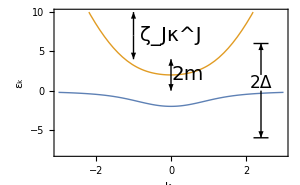

```mathematica
m=2;
energyscale2=Plot[{-(k^4+m^2)^(1/2)+k^2,(k^4+m^2)^(1/2)+k^2},{k,-3,3},PlotRange->{{-3,3},{-8,10}},Axes->False,
PlotStyle->Directive[Thick],Frame->True,FrameLabel->{Style["k_x",20],Style["ε_k",25]},FrameStyle->Directive[Thickness[0.007]],FrameTicks->{{None,None},{None,None}},RotateLabel->False,LabelStyle->Directive[Black,22],(*AspectRatio->0.7,*)Epilog->{Black,Arrowheads[0.05],Arrow[{{0,2},{0,4}}],Arrow[{{0,2},{0,0}}],Text[Style["2m",Italic,20],{0.45,2}],Arrow[{{-1,7},{-1,10}}],Arrow[{{-1,7},{-1,4}}],Text[Style["ζ_Jκ^J",20],{0,7}],Line[{{2.2,6},{2.6,6}}],Line[{{2.2,-6},{2.6,-6}}],Arrowheads[0.05],Arrow[{{2.4,2},{2.4,6}}],Arrow[{{2.4,0},{2.4,-6}}],Text[Style["2Δ",17],{2.4,1}]},ImageSize->300]
```

## Ds analytical

```mathematica
Integrate[-1/(x(4x+b)^(3/2)),x]
```

-2/(b √(b+4 x))+(2 ArcTanh[(√(b+4 x))/(√b)])/b^(3/2)

```mathematica
Integrate[1/(4x+b)^(3/2),x]
```

-1/(2 √(b+4 x))

## T_BKT estimation: crude model

```mathematica
dsfunction[delta_,egap_,dispwidth_]:=delta Log[(1+Sqrt[1+(2dispwidth/delta)^2])/(1+Sqrt[1+(egap/delta)^2])]
```

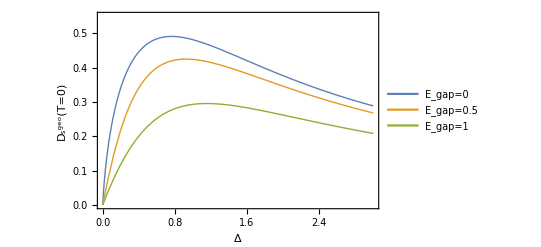

```mathematica
tbktplot1=Plot[{dsfunction[delta,0,1],dsfunction[delta,0.5,1],dsfunction[delta,1,1]},{delta,0,3},
PlotStyle->Thick,PlotRange->{{0,3},{0,0.55}},
Frame->True,FrameLabel->{{"D_s^geo(T=0)",None},{"Δ",None}},
FrameStyle->Directive[Thickness[0.007]],
LabelStyle->Directive[Black, 20],PlotLegends->Placed[LineLegend[{Style["E_gap=0",18],Style["E_gap=0.5",18],Style["E_gap=1",18]},LegendLayout->"Row"],{0.52,0.1}],ImageSize->400]
```

```mathematica
Export["tbktrough.pdf",tbktplot1]
```

tbktrough.pdf

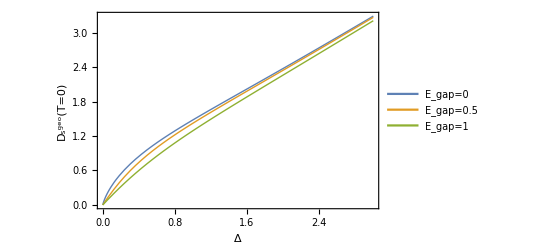

```mathematica
tbktplot1=Plot[{dsfunction[delta,0,1],dsfunction[delta,0.5,1],dsfunction[delta,1,1]},{delta,0,3},
PlotStyle->Thick,(*PlotRange->{{0,3},{0,0.55}},*)
Frame->True,FrameLabel->{{"D_s^geo(T=0)",None},{"Δ",None}},
FrameStyle->Directive[Thickness[0.007]],
LabelStyle->Directive[Black, 20],PlotLegends->Placed[LineLegend[{Style["E_gap=0",18],Style["E_gap=0.5",18],Style["E_gap=1",18]},LegendLayout->"Row"],{0.52,0.1}],ImageSize->400]
```

```mathematica
Solve[D[dsfunction[delta,egap,dispwidth],delta]==0,delta]
```

Solve[(delta (1+√(1+egap^2/delta^2)) (((1+√(1+(4 dispwidth^2)/delta^2)) egap^2)/(delta^3 √(1+egap^2/delta^2) (1+√(1+egap^2/delta^2))^2)-(4 dispwidth^2)/(delta^3 √(1+(4 dispwidth^2)/delta^2) (1+√(1+egap^2/delta^2)))))/(1+√(1+(4 dispwidth^2)/delta^2))+Log[(1+√(1+(4 dispwidth^2)/delta^2))/(1+√(1+egap^2/delta^2))]==0,delta]

Dirac point calculation

## analytical integral

```mathematica
Integrate[x(1+x^2)^(-3/2),x]
```

-1/(√(1+x^2))

## dirac point

```mathematica
dxdirac[kx_,ky_]:=kx/(kx^2+ky^2)^(1/2)
```

```mathematica
dydirac[kx_,ky_]:=ky/(kx^2+ky^2)^(1/2)
```

```mathematica
FullSimplify[D[dxdirac[kx,ky],kx]D[dxdirac[kx,ky],kx]+D[dydirac[kx,ky],kx]D[dydirac[kx,ky],kx]]
```

ky^2/((kx^2+ky^2)^2)

```mathematica
Integrate[(1/x)(1/Sqrt[x+1]-1/(x+1)^(3/2)),{x,0,a}]
```

ConditionalExpression[2-2/(√(1+a)),Re[a]>-1||a∉Reals]

```mathematica
Integrate[x/(x^2+1)^(3/2),{x,0,b}]
```

1-1/(√(1+b^2))

```mathematica
Integrate[1/(x(x^2+1)^(1/2))+1/(x(lambda^2 x^2+1)^(1/2))-(2/x)*(1/((x^2+1)^(1/2)+(lambda^2x^2+1)^(1/2)))(1+(1-lambda x^2)/((x^2+1)^(1/2)(lambda^2x^2+1)^(1/2))),{x,0,∞},Assumptions->Element[lambda,Positive]]
```

ConditionalExpression[1/(2 (-1+lambda^2))(1+lambda)^2 (-Log[1-lambda^2]+Log[-lambda^2+√(lambda^2)]+Log[lambda^2+√(lambda^2)]),Re[lambda]≠0]

```mathematica
Integrate[1/(x(x^2+1)^(1/2))+1/(x(lambda^2 x^2+1)^(1/2))-(2/x)*(1/((x^2+1)^(1/2)+(lambda^2x^2+1)^(1/2)))(1+(1-lambda x^2)/((x^2+1)^(1/2)(lambda^2x^2+1)^(1/2))),{x,0,a},Assumptions->Element[{lambda,a},Positive]]
```

ConditionalExpression[1/(2 (-1+lambda^2))(1+lambda)^2 (-2 Log[1+√(1+a^2)]-Log[1-lambda^2]+Log[1+(-1+√(1+a^2)) lambda^2+√(1+a^2 lambda^2)]+Log[1-(1+√(1+a^2)) lambda^2+√(1+a^2 lambda^2)]),Re[1/(a lambda)]≠0||Im[1/(a lambda)]>1||Im[1/(a lambda)]<-1]

```mathematica
lambda=0;
Integrate[1/(x(x^2+1)^(1/2))+1/(x(lambda^2 x^2+1)^(1/2))-(2/x)*(1/((x^2+1)^(1/2)+(lambda^2x^2+1)^(1/2)))(1+(1-lambda x^2)/((x^2+1)^(1/2)(lambda^2x^2+1)^(1/2))),{x,0,a}]
```

Log[1/2 (1+√(1+a^2))]

```mathematica
f1[lambda_,x_]:=x((lambda+1)/(lambda-1))Log[(1+Sqrt[1+lambda^2/x^2])/(1+Sqrt[1+1/x^2])]
```

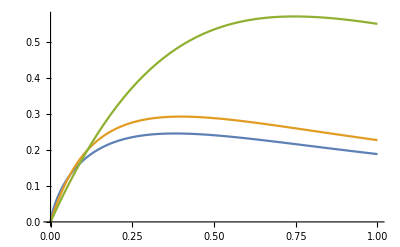

```mathematica
Plot[{f1[0,x],f1[0.1,x],f1[0.9,x]},{x,0,1}]
```

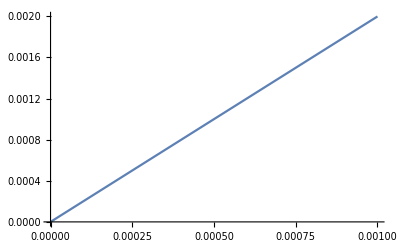

```mathematica
Plot[f1[0.999,x],{x,0,0.001}]
```

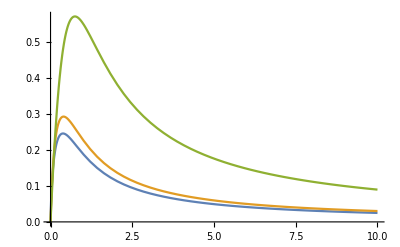

```mathematica
Plot[{f1[0,x],f1[0.1,x],f1[0.9,x]},{x,0,10}]
```

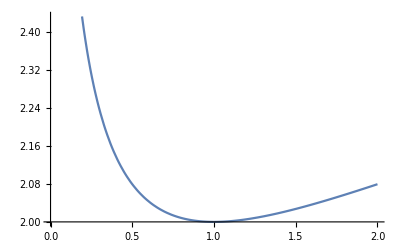

```mathematica
Plot[((x+1)/(x-1))Log[x],{x,0,2}]
```

```mathematica
Series[Log[(1+Sqrt[1+lambda^2 (1/x^2)])/(1+Sqrt[1+(1/x^2)])],{x,0,2}]
```

Log[(1+√(lambda^2/x^2))/(1+√(1/x^2))]+((-lambda^2 √(1/x^2)+√(lambda^2/x^2)+√(1/x^2) √(lambda^2/x^2)-lambda^2 √(1/x^2) √(lambda^2/x^2)) x^2)/(2 lambda^2 (1+√(1/x^2)) (1+√(lambda^2/x^2)))+O[x]^3

```mathematica
diracslope[lambda_]:=-((1+lambda)/(1-lambda))Log[Abs[lambda]]
```

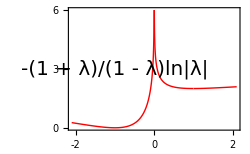

```mathematica
diracslopeplot=Plot[diracslope[lambda],{lambda,-2.1,2.1},PlotRange->{{-2.1,2.1},{0,6}},PlotStyle->Directive[Red,Thick],Frame->True,FrameLabel->{"λ",None},RotateLabel->False,LabelStyle->Directive[Black,20],FrameTicks->{{{0,3,6},None},{{-2,-1,0,1,2},None}},FrameStyle->Directive[Thickness[0.007]],Epilog->{Text[Style["-(1 + λ)/(1 - λ)ln|λ|",20],{-1,3}]},ImageSize->250]
```

```mathematica
Export["diracslope.pdf",diracslopeplot]
```

diracslope.pdf

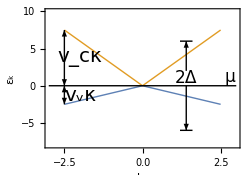

```mathematica
vv=-1;
vc=3;
diracplot=Plot[{vv Abs[k],vc Abs[k]},{k,-2.5,2.5},PlotRange->{{-3,3},{-8,10}},Axes->False,
PlotStyle->{Directive[Thick],Directive[Thick]},Frame->True,FrameLabel->{Style["k_x",20],Style["ε_k",25]},FrameStyle->Directive[Thickness[0.007]],FrameTicks->{{None,None},{None,None}},RotateLabel->False,LabelStyle->Directive[Black,22],AspectRatio->0.7,Epilog->{Line[{{-3,0},{3,0}}],Black,Arrowheads[0.04],Arrow[{{-2.5,-1.25},{-2.5,0}}],Arrow[{{-2.5,-1.25},{-2.5,-2.5}}],Text[Style["v_vκ",20],{-2,-1.25}],Arrowheads[0.05],Arrow[{{-2.5,3.75},{-2.5,7.5}}],Arrow[{{-2.5,3.75},{-2.5,0}}],Text[Style["v_cκ",20],{-2,3.75}],Line[{{1.2,6},{1.6,6}}],Line[{{1.2,-6},{1.6,-6}}],Arrowheads[0.05],Arrow[{{1.4,2},{1.4,6}}],Arrow[{{1.4,0},{1.4,-6}}],Text[Style["2Δ",17],{1.4,1}],Text[Style["μ",17],{2.8,1.2}]},ImageSize->250]
```

```mathematica
Export["diracplot.pdf",diracplot]
```

diracplot.pdf

```mathematica
diracds[λ_,delta_]:=(1/4π) delta ((1+λ)/(1-λ))Log[(1+Sqrt[1+1/delta^2])/(1+Sqrt[1+λ^2/delta^2])]
```

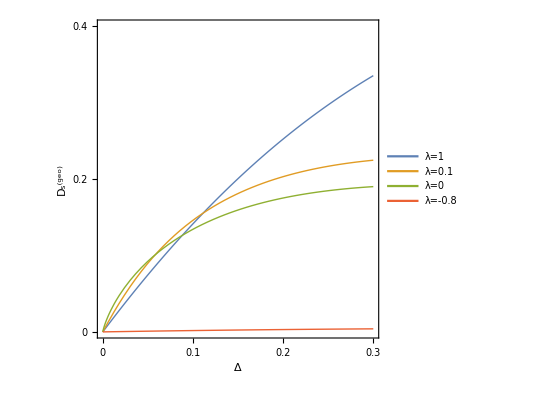

```mathematica
diracds1=Plot[{diracds[0.99,delta],diracds[0.1,delta],diracds[0,delta],diracds[-0.8,delta]},{delta,0,0.3},PlotRange->{{0,0.3},{0,0.4}},
PlotStyle->Directive[Thick],Frame->True,FrameLabel->{"Δ","D_s^(geo)"},RotateLabel->False,LabelStyle->Directive[Black,22],FrameTicks->{{{0,0.2,0.4},None},{{0,0.1,0.2,0.3},None}},FrameStyle->Directive[Thickness[0.007]],PlotLegends->Placed[LineLegend[{Style["λ=1",20],Style["λ=0.1",20],Style["λ=0",20],Style["λ=-0.8",20]},LegendLayout->{"Row",2}],{0.4,0.82}],AspectRatio->1]
```

```mathematica
Export["diracds1.pdf",diracds1]
```

diracds1.pdf

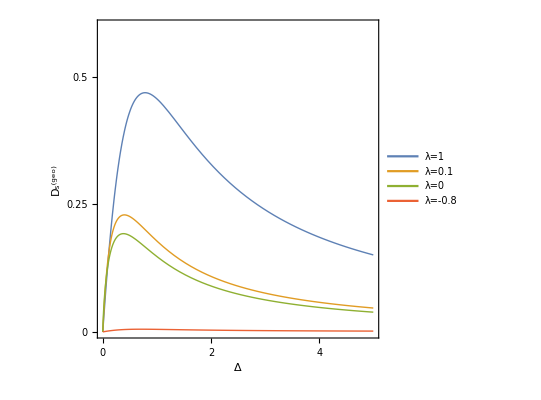

```mathematica
diracds2=Plot[{diracds[0.99,delta],diracds[0.1,delta],diracds[0,delta],diracds[-0.8,delta]},{delta,0,5},PlotRange->{{0,5},{0,0.6}},
PlotStyle->Directive[Thick],Frame->True,FrameLabel->{"Δ","D_s^(geo)"},RotateLabel->False,LabelStyle->Directive[Black,22],FrameTicks->{{{0,0.25,0.5},None},{{0,1,2,3,4,5},None}},FrameStyle->Directive[Thickness[0.007]],PlotLegends->Placed[LineLegend[{Style["λ=1",20],Style["λ=0.1",20],Style["λ=0",20],Style["λ=-0.8",20]},LegendLayout->{"Row",2}],{0.62,0.82}],AspectRatio->1]
```

```mathematica
Export["diracds2.pdf",diracds2]
```

diracds2.pdf